# BE/CS 196a Lab 06 Spectrofluorometry and error quantification of sample preparation

## Functions

excelLoad function reads an excel data file from a Synergy H1 plate reader, that contains two fluorescence datasets with distinct excitation and emission wavelengths, and generates two corresponding data lists in the format of {time, raw fluorescence}.
fileName is a string of the name of the data file including its extension (e.g. fileName = “data1.xlsx”).
col has two lists that each contains the left and right Excel column names of a dataset given as strings. For two fluorescence datasets of the same samples, these two lists are identify (e.g. col = {{“B”,“CU”},{“B”,“CU”}} covers all 96 samples in a plate).
row has two lists that each contains the top and bottom Excel rows of a dataset given as numbers, excluding the header.
delay is the delay time between the sample was mixed and the measurement was started (unit: hours).

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
excelLoad[fileName_,col_,row_,delay_]:=
Module[{rowRange,colRange,data,timeUnits,dataList},

rowRange=Range@@@row; 
colRange=Range@@@(Map[FromDigits[#,26]&,LetterNumber[Characters[col]],{2}]);

(*Load the Excel data*)
data=Import[fileName,{"Data",1,rowRange[[#]],Delete[colRange[[#]],2]}]&/@Range[Length[row]]; 

(* Rearrange data, Convert time stamps *)
(* Put data in (x, y) pairs of (time, value) *)
timeUnits=1/60/60; (* converts time to hours *)
dataList=Table[{N[(AbsoluteTime[data[[#]][[i]][[1]]]-AbsoluteTime[data[[#]][[1]][[1]]])*timeUnits+delay],data[[#]][[i]][[j]]},{j,2,Dimensions[data][[3]]},{i,Dimensions[data][[2]]}]&/@Range[Length[row]];

(*Return reshaped data*)
dataList]
```

PlotData function takes a list of data and plots multiple kinetics trajectories over time.
datalist is a list of trajectories, each containing a list of data points in the format of {time, raw fluorescence} or {time, concentration}.
trajectories is a list of species names or concentrations shown in the legend.
TrajectoryLabel is a label for the legend of trajectories. 
OutputLabel is a label for the vertical axis, which should be a description of the output measured. The unit of the data points should also be specified here. 
CircuitLabel is a label for the plot. It can be a description of the circuit. The default is none. 
TimeRange defines the range of time plotted. The unit is hours. The format is All, {All, max}, {min, All}, or {min, max}, where min and max should be given as the desired numbers for a time range.  The default is All (i.e. all data points plotted).
OutputRange defines the range of output plotted. The unit for raw data is arbitrary fluorescence level (a.u.). The unit for normalized data is nM. Same format and default as timeRange.

```mathematica
Options[PlotData]={plotSize->200,labelSize->12,pointSize->0.02};
PlotData[datalist_,trajectories_:"",TrajectoryLabel_:"",OutputLable_:"",CircuitLabel_:"",TimeRange_:All,OutputRange_:All,OptionsPattern[]]:=
ListPlot[datalist,PlotLabel->Style[CircuitLabel,OptionValue[labelSize]],
Frame->True,FrameLabel->{"Time (hours)",OutputLable},
PlotStyle->Table[{PointSize[OptionValue[pointSize]],ColorData["Rainbow"][i]},
{i,If[Length[datalist]<8,0.12,0],0.96,0.96/Length[datalist]}],
PlotLegends->Placed[SwatchLegend[Automatic,trajectories,LegendLabel->TrajectoryLabel,LegendMarkerSize->OptionValue[labelSize]*0.75],Right],
LabelStyle->Directive[Gray,FontSize->OptionValue[labelSize],FontFamily->"Helvetica"],
GridLines->Automatic,
PlotRange->{TimeRange,OutputRange},AspectRatio->1/1.3,ImageSize->OptionValue[plotSize]]
```

## Load data

Use excelLoad defined in Functions to load the Lab 06 data file into a data list. The delay time recorded from the experiment is 4 minutes.

```mathematica
list=excelLoad["Lab06_data.xlsx",{{"B","CU"},{"B","CU"}},{{47,62},{67,82}},4/60]
```

{{{{0.0666667,31.},{0.1,35.},{0.133333,35.},{0.166667,32.},{0.2,31.},{0.233333,43.},{0.266667,38.},{0.3,30.},{0.333333,44.},{0.366667,32.},{0.4,38.},{0.433333,38.},{0.466667,49.},{0.5,35.},{0.533333,31.},{0.566667,41.}},94,{{0.0666667,6102.},{0.1,6258.},13,{0.566667,6333.}}},{1}}
 |  |  |  |

Use built-in function Dimensions to verify the structure of the data list. The first number indicates two fluorescence channels. The second number indicates 96 samples in a plate (in order of wells A1 to A12, B1 to B12, etc.). The third number indicates 16 time point measurements. The last number indicates a data pair for each measurement (i.e. {time, raw fluorescence}).

```mathematica
Dimensions[list]
```

{2,96,16,2}

The samples from 8 students were organized in a 96-well plate as shown in the following diagram. Each row contains samples from a single student. The four samples from the calibration experiment were in columns 1 through 4, and the eight samples from the sample preparation practice were in columns 5 through 12.

-Graphics-

Separate the data of the calibration experiment and the sample preparation practice into two data lists based on their well positions, while separating each student's data into a sublist.

```mathematica
dataList1=Table[list[[All,1+12*x;;4+12*x,All,All]],{x,0,7}];
dataList2=Table[list[[All,5+12*x;;12+12*x,All,All]],{x,0,7}];
```

Again, use Dimensions to verify the structures of the two data lists.

```mathematica
Dimensions[dataList1]
Dimensions[dataList2]
```

{8,2,4,16,2}

{8,2,8,16,2}

In the following tasks, it will be helpful to use consistent and easy-to-remember variable names to access the relevant data points for each task. For example, if dataList1 is the data of the calibration experiment, one can use dataList1[[n,f,s,d,1]] and dataList1[[n,f,s,d,2]] to access the time and raw fluorescence of a data point, respectively, where n=1 to 8 is a student, f=1 or 2 is a fluorescence channel, s=1 to 4 is a sample, and d=1 to 16 is a data point.

## Generate a calibration formula

Use PlotData defined in Functions to display Student A’s raw fluorescence data of the calibration experiment. Examples on how to use this function were given in Lab 03.

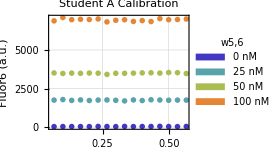

```mathematica
datalist6=dataList1[[1,1,All,All,All]];
trajectories={"0 nM", "25 nM", "50 nM", "100 nM"};
TrajectoryLabel="w5,6";
OutputLabel="Fluor6 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel="Student A Calibration";  
PlotData[datalist6,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

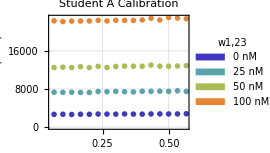

```mathematica
datalist23=dataList1[[1,2,All,All,All]];
trajectories={"0 nM", "25 nM", "50 nM", "100 nM"};
TrajectoryLabel="w1,23";
OutputLabel="Fluor23 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel="Student A Calibration";  
PlotData[datalist23,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

Use built-in function Mean to average the raw fluorescence levels over all 16 data points.

```mathematica
flour6=Table[Mean[dataList1[[1,1,x,All,2]]],{x,1,4}]
flour23=Table[Mean[dataList1[[1,2,x,All,2]]],{x,1,4}]
```

{36.4375,1746.44,3496.31,6951.19}

{2727.31,7425.88,12709.6,22468.6}

Then use built-in function LinearModelFit to apply a linear fit y = a + bx, where x is the average raw fluorescence of Fluor6 or Fluor23 and y is the concentration of signal strand w5,6 or w1,23.

```mathematica
xs={0,25,50,100}
data6=Table[{flour6[[i]],xs[[i]]},{i,1,4}]
data23=Table[{flour23[[i]],xs[[i]]},{i,1,4}]
flour6model=LinearModelFit[data6,x,x]
flour23model=LinearModelFit[data23,x,x]
```

{0,25,50,100}

{{36.4375,0},{1746.44,25},{3496.31,50},{6951.19,100}}

{{2727.31,0},{7425.88,25},{12709.6,50},{22468.6,100}}

FittedModel[-0.425222+0.0144477 x]

FittedModel[-13.3691+0.00504015 x]

Visualize the fitted function with the data, following the example on the documentation page of LinearModelFit. Use option FrameLabel to label the x and y axes, and use PlotLabel to display the calibration formula.

-0.425222+0.0144477 x

-13.3691+0.00504015 x

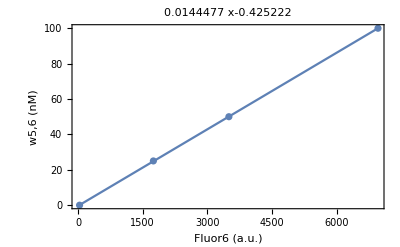

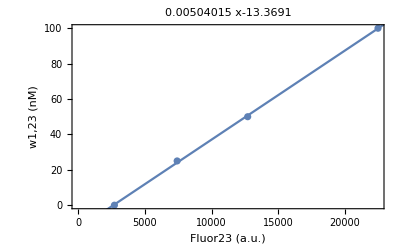

```mathematica
eq6=Normal[flour6model]
eq23=Normal[flour23model]
Show[ListPlot[data6],Plot[flour6model[x],{x,0,7000}],Frame->True,FrameLabel->{"Fluor6 (a.u.)","w5,6 (nM)"},PlotLabel->eq6]
Show[ListPlot[data23],Plot[flour23model[x],{x,0,25000}],Frame->True,FrameLabel->{"Fluor23 (a.u.)","w1,23 (nM)"},PlotLabel->eq23]
```

## Quantify the errors of sample preparation by a single student

Display Student A’s raw fluorescence data of the sample preparation practice.

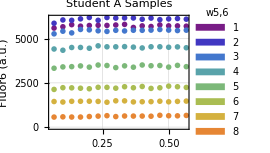

```mathematica
samplelist6=dataList2[[1,1,All,All,All]];
trajectories={"1","2","3","4","5","6","7","8"};
TrajectoryLabel="w5,6";
OutputLabel="Fluor6 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel="Student A Samples";  
PlotData[samplelist6,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

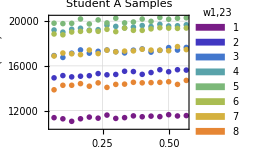

```mathematica
samplelist23=dataList2[[1,2,All,All,All]];
trajectories={"1","2","3","4","5","6","7","8"};
TrajectoryLabel="w1,23";
OutputLabel="Fluor23 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel="Student A Samples";  
PlotData[samplelist23,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

Use the two calibration formulas established above to convert/normalize the raw fluorescence data to concentration data.

```mathematica
conc6=Table[{dataList2[[1,1,i,j,1]],flour6model[dataList2[[1,1,i,j,2]]]},{i,1,8},{j,1,16}];
conc23=Table[{dataList2[[1,2,i,j,1]],flour23model[dataList2[[1,2,i,j,2]]]},{i,1,8},{j,1,16}];
```

Display the concentration data.

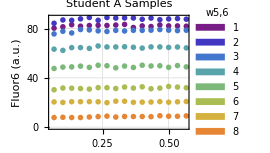

```mathematica
trajectories={"1","2","3","4","5","6","7","8"};
TrajectoryLabel="w5,6";
OutputLabel="Fluor6 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel="Student A Samples";  
PlotData[conc6,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

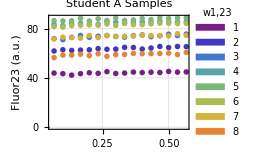

```mathematica
trajectories={"1","2","3","4","5","6","7","8"};
TrajectoryLabel="w1,23";
OutputLabel="Fluor23 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel="Student A Samples";  
PlotData[conc23,trajectories,TrajectoryLabel,OutputLabel,CircuitLabel]
```

Convert the concentration data of each sample to a single pair of data points {x,y}, where x is the average concentration of Fluor6 and y is the average concentration of Fluor23.

```mathematica
aveFlour=Table[{Mean[conc6[[i,All,2]]],Mean[conc23[[i,All,2]]]},{i,1,8}]
```

{{82.222,44.1368},{87.7672,63.8299},{78.248,73.8106},{64.6166,84.6117},{49.1792,87.6222},{31.7896,83.3104},{20.4969,73.8257},{8.44928,59.0496}}

Use ListPlot to display all pairs of average concentrations on a square grid of Fluor6 and Fluor23 ranging from 0 to 100 nM. You may use option PlotRange to specify the range of coordinates, AspectRatio→1 to specify a square plot, and GridLines→Full to specify a full grid. As usual, FrameLabel and LabelStyle are useful for adding necessary information on the plot.

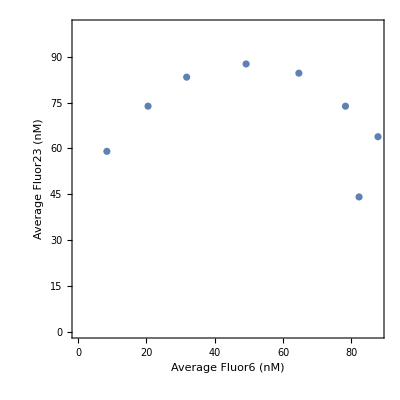

```mathematica
ListPlot[aveFlour,PlotRange->{0,100},Frame->True,FrameLabel->{"Average Fluor6 (nM)","Average Fluor23 (nM)"},AspectRatio->1,GridLines->Full,LabelStyle->Directive[Gray,FontSize->12,FontFamily->"Helvetica"]]
```

Now let us compare the measured concentrations with the designed concentrations of the sample preparation practice, which are eight points on a circle. For students A, C, E, and G, all designed points are on the top half of the circle; for students B, D, F, and H, all designed points are on the bottom half of the circle. The designed points are given as follows:

```mathematica
topCirclePoints=Table[CirclePoints[{50,50},{40,0},16][[s]],{s,8}];
bottomCirclePoints=Table[CirclePoints[{50,50},{40,0},16][[s]],{s,9,16}];
```

Display the measured and designed concentrations in two distinct colors on the same square grid, with a Line connecting each data point to its design. You may also use Circle to display a half circle on top of the points.  The built-in function Show allows for the display of a ListPlot overlaid with a Graphics. As usual, PlotLegends is useful for adding necessary information on the plot, as shown in the third example on the documentation page of ListPlot.

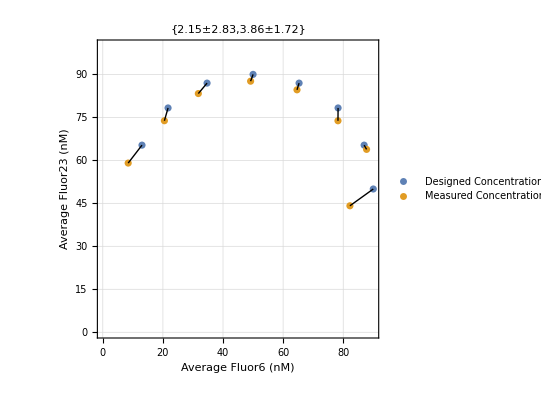

```mathematica
Show[ListPlot[{topCirclePoints,aveFlour},PlotRange->{0,100},Frame->True,FrameLabel->{"Average Fluor6 (nM)","Average Fluor23 (nM)"},PlotLegends->{"Designed Concentrations","Measured Concentration"},AspectRatio->1,GridLines->Full,LabelStyle->Directive[Gray,FontSize->12,FontFamily->"Helvetica"],PlotLabel->{ PlusMinus[meanErr[[1]],stdErr[[1]]], PlusMinus[meanErr[[2]],stdErr[[2]]]}],Graphics[Line[Table[{aveFlour[[i]],topCirclePoints[[i]]},{i,1,Length[aveFlour]}]]]]
```

Essentially, the difference between the data points and the design indicate experimental error. Calculate the mean and standard deviation of errors across all eight data points, while keeping the x- and y-coordinate (i.e. Fluor6 and Fluor23) errors separate. Round the mean and standard deviation to keep 2 digits after the decimal points. Note that the sign of the error matters here, as it may indicate systematic errors below or above the designed values (e.g. if the errors are half positive and half negative, the mean should be close to 0; if the errors are mostly negative, the mean should be negative).

```mathematica
meanErr=Round[Mean[topCirclePoints-aveFlour],0.01]
```

{2.15,3.86}

```mathematica
stdErr=Round[StandardDeviation[topCirclePoints-aveFlour],0.01]
```

{2.83,1.72}

Display the calculated errors, as mean ± standard deviation, on the above plot using PlotLabel .

## Quantify the errors of sample preparation across all students

Display all students’ raw fluorescence data of the calibration experiment.

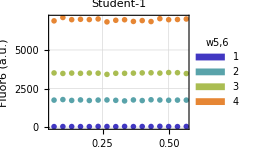
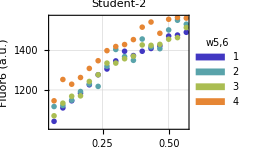
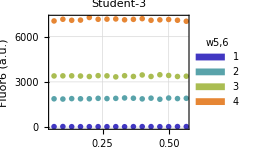
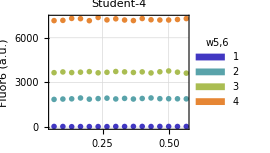
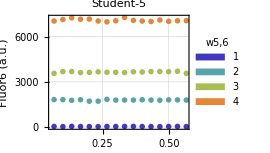
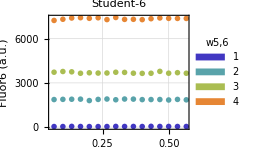
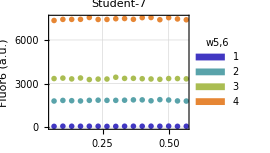
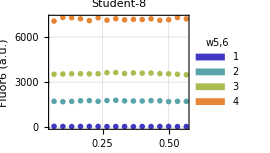

```mathematica
calibrationAll6=Table[dataList1[[i,1,All,All,All]],{i,1,8}];
trajectories={"1","2","3","4","5","6","7","8"};
TrajectoryLabel="w5,6";
OutputLabel="Fluor6 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel=Table["Student"-i,{i,1,8}];  
plots=Table[PlotData[calibrationAll6[[i]],trajectories,TrajectoryLabel,OutputLabel,CircuitLabel[[i]]],{i,1,8}]
```

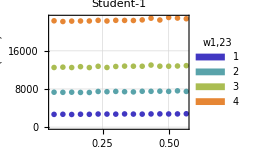
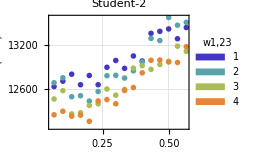
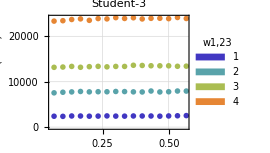
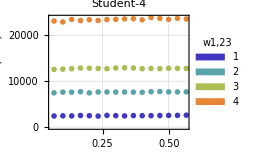
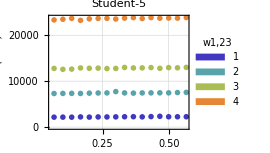
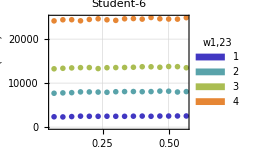
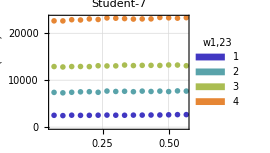
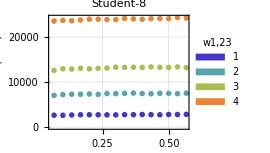

```mathematica
calibrationAll23=Table[dataList1[[i,2,All,All,All]],{i,1,8}];
trajectories={"1","2","3","4","5","6","7","8"};
TrajectoryLabel="w1,23";
OutputLabel="Fluor23 (a.u.)"; (* the unit for raw data is arbitrary fluorescence level (a.u.) *)
CircuitLabel=Table["Student"-i,{i,1,8}];  
plots=Table[PlotData[calibrationAll23[[i]],trajectories,TrajectoryLabel,OutputLabel,CircuitLabel[[i]]],{i,1,8}]
```

Fit each student’s data to determine a calibration formula, and display all 8 fitted functions with the data.

```mathematica
flourAll6=Table[Table[Mean[dataList1[[i,1,x,All,2]]],{x,1,4}],{i,1,8}];
flourAll23=Table[Table[Mean[dataList1[[i,2,x,All,2]]],{x,1,4}],{i,1,8}];
```

```mathematica
xs={0,25,50,100};
```

```mathematica
dataAll6=Table[Table[{flourAll6[[i]][[j]],xs[[j]]},{j,1,4}],{i,1,8}];
dataAll23=Table[Table[{flourAll23[[i]][[j]],xs[[j]]},{j,1,4}],{i,1,8}];
```

```mathematica
flour6Allmodel=Table[LinearModelFit[dataAll6[[i]],x,x],{i,1,8}];
flour23Allmodel=Table[LinearModelFit[dataAll23[[i]],x,x],{i,1,8}];
```

```mathematica
eqAll6=Table[Normal[flour6Allmodel[[i]]],{i,1,8}];
eqAll23=Table[Normal[flour23Allmodel[[i]]],{i,1,8}];
```

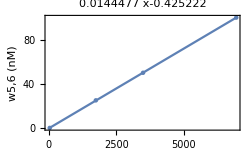
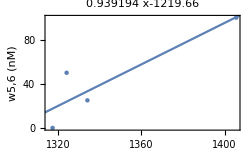
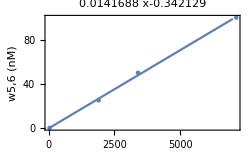
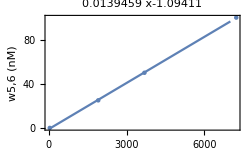
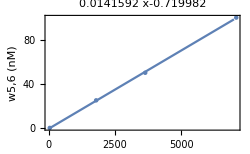
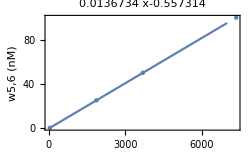
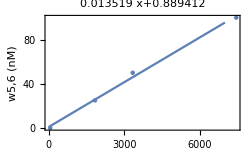
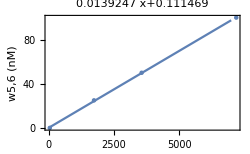

```mathematica
Table[Show[ListPlot[dataAll6[[i]]],Plot[flour6Allmodel[[i]][x],{x,0,7000}],ImageSize->250,Frame->True,FrameLabel->{"Fluor6 (a.u.)","w5,6 (nM)"},PlotLabel->eqAll6[[i]]],{i,1,8}]
Table[Show[ListPlot[dataAll23[[i]]],Plot[flour23Allmodel[[i]][x],{x,0,25000}],ImageSize->250,Frame->True,FrameLabel->{"Fluor23 (a.u.)","w1,23 (nM)"},PlotLabel->eqAll23[[i]]],{i,1,8}]
```

Use each student’s calibration formula to normalize their raw fluorescence data of the sample preparation practice to concentration data, convert the concentration data to data points on a circle, and calculate each of their errors. If any student’s calibration formula was obviously wrong, use another student’s formula instead.

```mathematica
flour6Allmodel[[2]]=flour6Allmodel[[1]];
flour23Allmodel[[2]]=flour23Allmodel[[1]];
```

```mathematica
concAll6=Table[Table[{dataList2[[k,1,i,j,1]],flour6Allmodel[[k]][dataList2[[k,1,i,j,2]]]},{i,1,8},{j,1,16}],{k,1,8}];
concAll23=Table[Table[{dataList2[[k,2,i,j,1]],flour23Allmodel[[k]][dataList2[[k,2,i,j,2]]]},{i,1,8},{j,1,16}],{k,1,8}];
```

```mathematica
aveAllFlour=Table[Table[{Mean[concAll6[[j,i,All,2]]],Mean[concAll23[[j,i,All,2]]]},{i,1,8}],{j,1,8}];
```

```mathematica
meanAllErrTop=Table[Round[Mean[topCirclePoints-aveAllFlour[[i]]],0.01],{i,1,8,2}];
meanAllErrBottom=Table[Round[Mean[bottomCirclePoints-aveAllFlour[[i]]],0.01],{i,2,8,2}];
stdAllErrTop=Table[Round[StandardDeviation[topCirclePoints-aveAllFlour[[i]]],0.01],{i,1,8,2}];
stdAllErrBottom=Table[Round[StandardDeviation[bottomCirclePoints-aveAllFlour[[i]]],0.01],{i,2,8,2}];
```

Display all students’ circle data overlaid with design and labeled with errors.

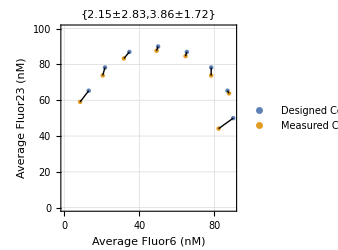
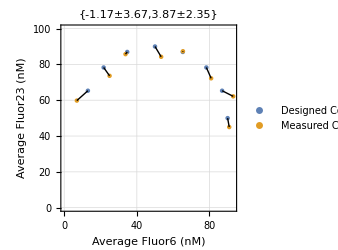
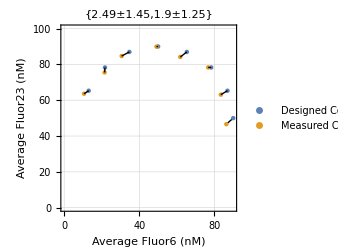
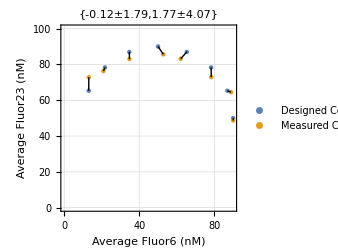

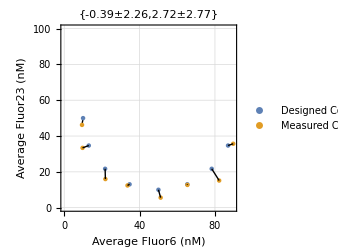
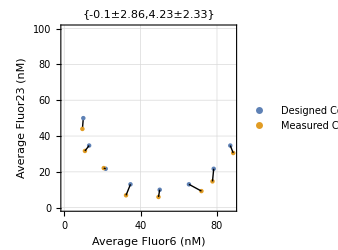
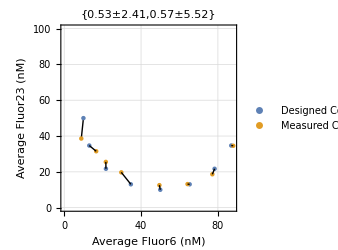
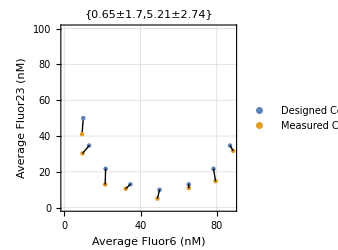

```mathematica
Table[Show[ListPlot[{topCirclePoints,aveAllFlour[[j]]},PlotRange->{0,100},Frame->True,FrameLabel->{"Average Fluor6 (nM)","Average Fluor23 (nM)"},PlotLegends->{"Designed Concentrations","Measured Concentration"},ImageSize->250,AspectRatio->1,GridLines->Full,LabelStyle->Directive[Gray,FontSize->12,FontFamily->"Helvetica"],PlotLabel->{ PlusMinus[meanAllErrTop[[(j+1)/2]][[1]],stdAllErrTop[[(j+1)/2]][[1]]], PlusMinus[meanAllErrTop[[(j+1)/2]][[2]],stdAllErrTop[[(j+1)/2]][[2]]]}],Graphics[Line[Table[{aveAllFlour[[j]][[i]],topCirclePoints[[i]]},{i,1,Length[aveAllFlour[[j]]]}]]]],{j,1,8,2}]
Table[Show[ListPlot[{bottomCirclePoints,aveAllFlour[[j]]},PlotRange->{0,100},Frame->True,FrameLabel->{"Average Fluor6 (nM)","Average Fluor23 (nM)"},PlotLegends->{"Designed Concentrations","Measured Concentration"},ImageSize->250,AspectRatio->1,GridLines->Full,LabelStyle->Directive[Gray,FontSize->12,FontFamily->"Helvetica"],PlotLabel->{ PlusMinus[meanAllErrBottom[[j/2]][[1]],stdAllErrBottom[[j/2]][[1]]], PlusMinus[meanAllErrBottom[[j/2]][[2]],stdAllErrBottom[[j/2]][[2]]]}],Graphics[Line[Table[{aveAllFlour[[j]][[i]],bottomCirclePoints[[i]]},{i,1,Length[aveAllFlour[[j]]]}]]]],{j,2,8,2}]
```

What is the average Fluor6 and Fluor23 errors across all students?

```mathematica
meanMean=Mean[(meanAllErrTop+meanAllErrBottom)/2];
meanStd=Mean[(stdAllErrTop+stdAllErrBottom)/2];
error6=PlusMinus[meanMean[[1]],meanStd[[1]]]
error23=PlusMinus[meanMean[[2]],meanStd[[2]]]
```

0.505±2.37125

3.01625±2.84375

When differences occur between experimental data and expected molecular behavior based on the design, there are typically two types of possibilities: experimental errors and unexpected molecular behaviors. Compare the means and standard deviations of the Fluor6 and Fluor23 errors, what do you think the differences here might suggest?

This is likely to be because of unexpected molecular behaviors. Since the standard deviations are similar, but the means are different for the Fluor6 and Fluor23 errors, experimental errors are likely not the issue, so the difference is likely due to molecular behaviors.

Could you find clues in the raw fluorescence data that would lead to a hypothesis?

The raw fluorescence data also indicates that it likely due to unexpected molecular behaviors. The experimental error in very similar between the Fluor6 and Fluor23, so it is unlikely that experimental error would explain the difference in mean error between Fluor6 and Fluor23. It seems more likely that the difference in scale between Fluor6 (up to 7000) and Fluor23 (up to 25000) would cause the difference in mean errors.

Is there any adjustment in quantifying the errors that could help verify your hypothesis?

We might be able to get rid of the difference in errors by normalizing the fluorescence data to the same scale first before converting it to concentration data.